```mathematica
f[n_]:=3n+1/;Mod[n,2]==1;
f[n_]:=n/2/;Mod[n,2]==0;
```

```mathematica
Manipulate[a=t;i=1;
b={};
While[a≠ 1,b=b∪{{i,a}};a=f[a];i++];
ListLinePlot[b,PlotRange->{{0,Max[b[[All,1]]]},{0,Max[b[[All,2]]]}}],{t,3,3001,2}]
```

```mathematica
FN2[n_]:=2n;
FN3[n_]:=(n-1)/3/;Mod[n,3]==1;
FN3[n_]:=2n/;Mod[n,3]≠ 1;
```

```mathematica
FN3[7]
```

2

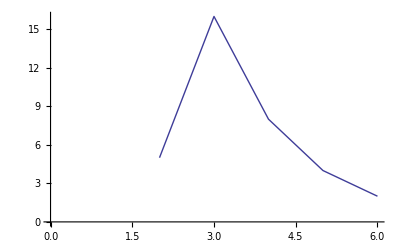

({1,0,1}
{1,0,0,0,0}
{1,0,0,0}
{1,0,0}
{1,0})

{2,1,1,1,1}

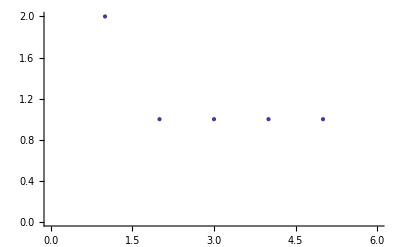

```mathematica
a=10;i=1;
c={};
While[a≠ 1,If[Mod[a,2]==1 || Total[IntegerDigits[a,2]]==1,c=c∪{{i,a}},c=c];a=f[a];i++];
ListLinePlot[c,PlotRange->{{0,Max[c[[All,1]]]},{0,Max[c[[All,2]]]}}]
d=IntegerDigits[c[[All,2]],2]//MatrixForm
Total[%,{-1}]
ListPlot[%,PlotRange->{{0,Max[c[[All,1]]]},{0,Max[%]}}]
```

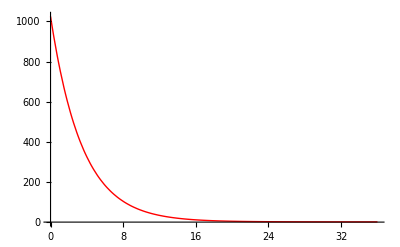

```mathematica
Plot[(b-1) (3/4)^x+1,{x,0,Max[c[[All,1]]]},PlotStyle->Red,PlotRange->Full]
```

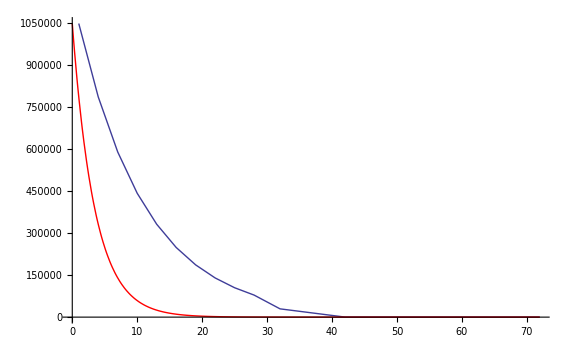

({1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}
{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}
{1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}
{1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1}
{1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1}
{1,1,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,1}
{1,0,1,1,0,1,1,0,0,1,0,0,0,0,0,0,0,1}
{1,0,0,0,1,0,0,0,1,0,1,1,0,0,0,0,0,1}
{1,1,0,0,1,1,0,1,0,0,0,0,1,0,0,0,1}
{1,0,0,1,1,0,0,1,1,1,0,0,0,1,1,0,1}
{1,1,1,0,0,1,1,0,1,0,1,0,1,0,1}
{1,0,1,0,1,1,0,1}
{1,0,0,0,0,0,1}
{1,1,0,0,0,1}
{1,0,0,1,0,1}
{1,1,1}
{1,0,1,1}
{1,0,0,0,1}
{1,1,0,1}
{1,0,1}
{1,0,0,0,0}
{1,0,0,0}
{1,0,0}
{1,0})

{2,3,3,5,4,7,7,6,7,9,9,5,2,3,3,3,3,2,3,2,1,1,1,1}

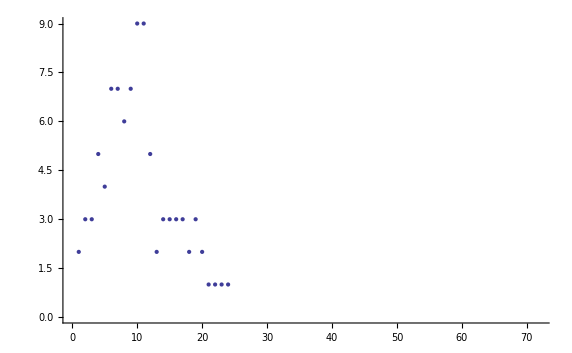

```mathematica
a=2^20+1;i=1;b=a;
c={};
While[a≠ 1,If[Mod[a,2]==1 || Total[IntegerDigits[a,2]]==1,c=c∪{{i,a}},c=c];a=f[a];i++];
Show[ListLinePlot[c,PlotRange->{{0,Max[c[[All,1]]]},{0,Max[c[[All,2]]]}}],Plot[(b-1) (3/4)^x+1,{x,0,Max[c[[All,1]]]},PlotStyle->Red,PlotRange->Full]]
d=IntegerDigits[c[[All,2]],2]//MatrixForm
Total[%,{-1}]
ListPlot[%,PlotRange->{{0,Max[c[[All,1]]]},{0,Max[%]}}]
```

```mathematica
Table[{BaseForm[2^n,6],BaseForm[(2^(2n)-1)/3,6],BaseForm[(2^(6n+2)-4)/9,6]},{n,1,27}]//MatrixForm
```

(2_6 | 1_6 | 44_6
4_6 | 5_6 | 12232_6
12_6 | 33_6 | 2255220_6
24_6 | 221_6 | 423453004_6
52_6 | 1325_6 | 115204241152_6
144_6 | 10153_6 | 22010352500140_6
332_6 | 41141_6 | 4053545421225524_6
1104_6 | 245045_6 | 1122022050350350112_6
2212_6 | 1512313_6 | 210500105025024541100_6
4424_6 | 11254101_6 | 35205220101021004442444_6
13252_6 | 45544405_6 | 10530532534551505230335032_6
30544_6 | 315510433_6 | 2014535312050434534502502020_6
101532_6 | 2115243021_6 | 335124150225041244034101535404_6
203504_6 | 12513500125_6 | 102515255402223313354323124203552_6
411412_6 | 55303200553_6 | 15304423523213534510124303302302540_6
1223224_6 | 354021203541_6 | 3225223213520140035103321012424512324_6
2450452_6 | 2344125223445_6 | 1002253520132545450511415510331355512512_6
5341344_6 | 14304553343113_6 | 144423212544514055451342103141454343543500_6
15123132_6 | 110031542300501_6 | 31103115553520202340011431350152532141325244_6
34250304_6 | 440211454003205_6 | 5403342115212554035042144252552231202125101432_6
112541012_6 | 3041251144021233_6 | 1403423434011555234503443035034535021555431104420_6
225522024_6 | 20245525104125421_6 | 255435201110211500034242410502444100051532204022204_6
455444052_6 | 121515352424554525_6 | 51533325404315353210353124410055002413243210312130352_6
1355332144_6 | 531314334551551353_6 | 13243421124003241515145503340254212445245235134240105340_6
3155104332_6 | 3410110231531530341_6 | 2445314331225005000403302223131303535222020121152300155124_6
10354213104_6 | 22440441411411402245_6 | 455231045430213252111412413504241100133255342340144033035312_6
21152430212_6 | 135043050450450413513_6 | 125055000452040050512541125330352442425011515515110554130550300_6)